I need plots of time taken vs T and dt as well as plot for Objective Cost vs T and and maybe dt

Points below: 
data = ((T,dt,{J,time (sec),iterations}), ... )
data1=((T,dt,J), ... )
data2=((T,dt,time), ... )
data3=((T,dt,iterations), ... )

```mathematica
data={{4,.01,{2234.9,793.86,1234}},{5,.01,{6189.2,1309.8,1052}},{6,.01,{4001.2,2751.1,1346}},{4,.003,{2214.6,41349.0,2225}},{5,.003,{3980.5,49026.4,853}},{6,.003,{6165.7,77169.9,933}},{4,.004,{2217.5,17795.7,2299}},{5,.004,{3984.0,4011.3,239}},{6,.004,{5727.7,15909.1,308}},{4,.005,{2220.3,10141.4,2465}},{5,.005,{3986.8,1904.2,201}},{6,.005,{5738.3,6328.1,251}}};
data1=data;
data2=data;
data3=data;
data1[[;;,3]]=data[[;;,3]][[;;,1]];
data2[[;;,3]]=data[[;;,3]][[;;,2]]/(60*60);
data3[[;;,3]]=data[[;;,3]][[;;,3]];
data1
data2
data3
```

{{4,0.01,2234.9},{5,0.01,6189.2},{6,0.01,4001.2},{4,0.003,2214.6},{5,0.003,3980.5},{6,0.003,6165.7},{4,0.004,2217.5},{5,0.004,3984.},{6,0.004,5727.7},{4,0.005,2220.3},{5,0.005,3986.8},{6,0.005,5738.3}}

{{4,0.01,0.220517},{5,0.01,0.363833},{6,0.01,0.764194},{4,0.003,11.4858},{5,0.003,13.6184},{6,0.003,21.4361},{4,0.004,4.94325},{5,0.004,1.11425},{6,0.004,4.41919},{4,0.005,2.81706},{5,0.005,0.528944},{6,0.005,1.75781}}

{{4,0.01,1234},{5,0.01,1052},{6,0.01,1346},{4,0.003,2225},{5,0.003,853},{6,0.003,933},{4,0.004,2299},{5,0.004,239},{6,0.004,308},{4,0.005,2465},{5,0.005,201},{6,0.005,251}}

```mathematica
ListPlot3D[data1,Mesh->None,InterpolationOrder->3,ColorFunction->"SunsetColors",ImageSize->Large]

ListPlot3D[data2,Mesh->None,InterpolationOrder->3,ColorFunction->"SunsetColors",ImageSize->Large,PlotRange->Full]

ListDensityPlot[data1,Mesh->None,InterpolationOrder->3,ColorFunction->"SolarColors",PlotLegends->Automatic,ImageSize->Large]

ListDensityPlot[data2,Mesh->None,InterpolationOrder->3,ColorFunction->"SolarColors",PlotLegends->Automatic,ImageSize->Large,PlotRange->Full]

ListDensityPlot[data1,Mesh->None,InterpolationOrder->3,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,ImageSize->Large]

ListDensityPlot[data2,Mesh->None,InterpolationOrder->3,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

-Graphics3D-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

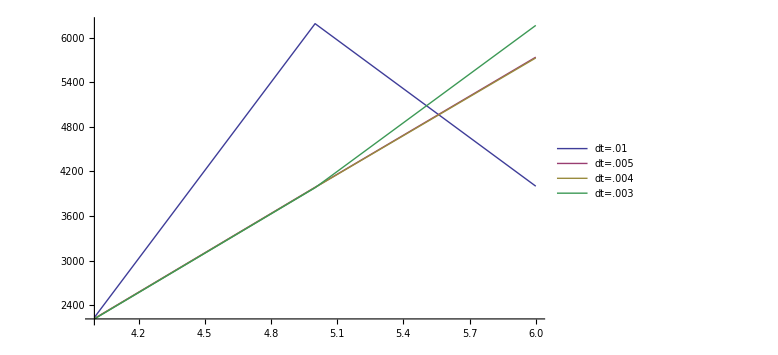

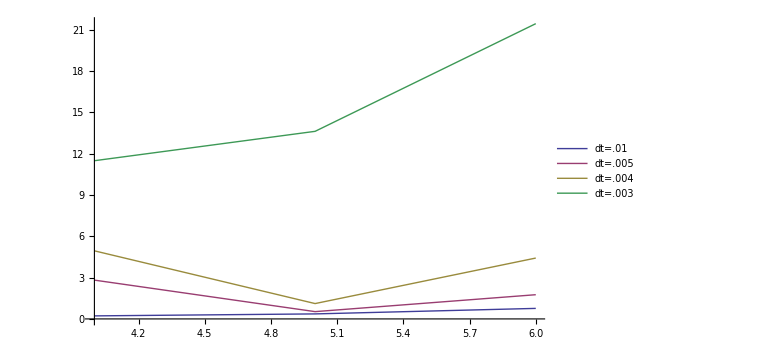

```mathematica
(* Objective Cost vs time horizon for different dt *)
ListLinePlot[{data1[[Length[data1]-11;;Length[data1]-9,{1,3}]],data1[[Length[data1]-2;;Length[data1],{1,3}]],data1[[Length[data1]-5;;Length[data1]-3,{1,3}]],data1[[Length[data1]-8;;Length[data1]-6,{1,3}]]},PlotStyle->Thick,PlotLegends->{"dt=.01","dt=.005","dt=.004","dt=.003"},ImageSize->Large]

(* Calculation time (hours) vs time horizon for different dt *)
ListLinePlot[{data2[[Length[data2]-11;;Length[data2]-9,{1,3}]],data2[[Length[data2]-2;;Length[data2],{1,3}]],data2[[Length[data2]-5;;Length[data2]-3,{1,3}]],data2[[Length[data2]-8;;Length[data2]-6,{1,3}]]},PlotStyle->Thick,PlotLegends->{"dt=.01","dt=.005","dt=.004","dt=.003"},ImageSize->Large]
```

```mathematica
data1[[Length[data1]-8;;Length[data1]-6,{1,2,3}]]
```

{{4,0.003,2214.6},{5,0.003,3980.5},{6,0.003,6165.7}}